# Load packages

```mathematica
SetDirectory[NotebookDirectory[]<>"../../package/"];
Get["funcs_rxns_moms.m"]
```

# Setup

```mathematica
nv=3;
nh=1;

volExp=14;
cdir="../../"<>getCacheDirRaw[volExp];

SetDirectory[NotebookDirectory[]];
dataDesc=importDataDesc[cdir<>"data_desc.txt"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
{mv,sv}=Import[cdir<>"transformations.txt","Table"]
```

{{1749.78,6454.46,2550.},{1392.37,5856.93,2450.}}

# Import

## Data

```mathematica
SetDirectory[NotebookDirectory[]];

noIP3Rs={100,500,600,700,800,900,1000,1500,2000,2500,3000,3500,4000,4500,5000};
ip3s={
"ip3_0p100","ip3_0p200","ip3_0p300","ip3_0p400","ip3_0p500","ip3_0p600","ip3_0p700","ip3_0p800","ip3_0p900","ip3_1p000",
"ip3_1p100","ip3_1p200","ip3_1p300","ip3_1p400","ip3_1p500","ip3_1p600","ip3_1p700","ip3_1p800","ip3_1p900","ip3_2p000"
};

ip3Keys={};
Do[
Do[
AppendTo[ip3Keys,{noIP3R,ip3}]
,{ip3,ip3s}];
,{noIP3R,noIP3Rs}];

filtered0=Association[];
derivs0=Association[];

Monitor[
Do[
{noIP3R,ip3}=ip3Keys[[iKey]];
cdir="../../"<>getCacheDirRaw[volExp,noIP3R];

pLFDL=Association[];
Do[
pLFDL[k]=Flatten[Import[cdir<>"filtered0/"<>ip3<>"/"<>k<>".txt","Table"]]
,{k,makeLF[nv,nh]}];

filtered0[ip3Keys[[iKey]]]=makePStructFromLFDL[nv,nh,pLFDL];

pLFDL=Association[];
Do[
pLFDL[k]=Flatten[Import[cdir<>"derivs0/"<>ip3<>"/"<>k<>".txt","Table"]]
,{k,makeLF[nv,nh]}];

derivs0[ip3Keys[[iKey]]]=makePStructFromLFDL[nv,nh,pLFDL];

,{iKey,Length[ip3Keys]}];
,ProgressIndicator[iKey,{1,Length[ip3Keys]}]];
```

## Training data

```mathematica
graphInputsWOSTD=Association[];
rxnsSTDm=Association[];
rxnsSTDv=Association[];

SetDirectory[NotebookDirectory[]];
tdir="../training_data/training_data/";

outMean=Flatten[Import[tdir<>"out_mean.txt","Table"]];
outStd=Flatten[Import[tdir<>"out_std.txt","Table"]];

trainingDataS=Import[tdir<>"training_data_s.mx"];
validationDataS=Import[tdir<>"validation_data_s.mx"];

ip3KeysTraining=Import[tdir<>"ip3_keys_train.txt","Table"];
ip3KeysValidation=Import[tdir<>"ip3_keys_test.txt","Table"];

Do[
graphInputsWOSTD[mode]=Import[tdir<>"graph_"<>mode<>"_inputs_wo_std.wlnet"];

rxnsSTDm[mode]=Flatten[Import[tdir<>"std_"<>mode<>"_m.txt","Table"]];
rxnsSTDv[mode]=Flatten[Import[tdir<>"std_"<>mode<>"_v.txt","Table"]];

,{mode,{"params","rxns"}}];
```

# Make graphs & export

```mathematica
makeGraph[graphInputsWOSTD_,subNet_,STDm_,STDv_]:=Module[
{layerDefns,layerConn,graph,rxnName,idx}
,
layerDefns=<|
"inputsWOSTD"->graphInputsWOSTD,

"subNet"->subNet,

"STDmean"->NetArrayLayer["Array"->STDm,LearningRateMultipliers->None],
"STDstd"->NetArrayLayer["Array"->STDv,LearningRateMultipliers->None],
"STD"->FunctionLayer[(#in-#mean)/#std&,"in"->Length[STDm],"mean"->Length[STDm],"std"->Length[STDm]],
"STDremoveZeros"->ElementwiseLayer[If[Abs[#]>1.*10^-5,#,0.0]&]
|>;

layerConn={
"STDmean"->NetPort["STD","mean"],
"STDstd"->NetPort["STD","std"],
"inputsWOSTD"->NetPort["STD","in"],

"STD"->"STDremoveZeros"->"subNet"
};

Return[NetGraph[layerDefns,layerConn]];
]
```

```mathematica
noOutput=2;
subNet=NetChain[{
150,Ramp,DropoutLayer[0.1],
150,Ramp,DropoutLayer[0.1],
150,Ramp,DropoutLayer[0.1],
150,Ramp,DropoutLayer[0.1],
150,Ramp,DropoutLayer[0.1],
noOutput}];

graphs=Association[];
Do[
graphs[mode]=makeGraph[graphInputsWOSTD[mode],subNet,rxnsSTDm[mode],rxnsSTDv[mode]]
,{mode,{"rxns","params"}}];
```

## Export

```mathematica
SetDirectory[NotebookDirectory[]];
Export["trained/sub_net.wlnet",subNet]

Do[
Export["trained/"<>k<>"/graph_not_trained.wlnet",graphs[k]]
,{k,Keys[graphs]}]
```

trained/sub_net.wlnet

# Import graphs

```mathematica
SetDirectory[NotebookDirectory[]];
subNet=Import["trained/sub_net.wlnet"];

graphs=Association[];
Do[
graphs[k]=Import["trained/"<>k<>"/graph_not_trained.wlnet"]
,{k,{"rxns","params"}}]
```

# Train nets & export

```mathematica
modesRun={"params","rxns"};
runStart=27;
runEnd=40;

maxTrainingRounds=25;
method={"ADAM","WeightClipping"->0.5};
```

```mathematica
Do[
Print[iNet];

Do[
Print[mode];
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ["trained/"<>mode],CreateDirectory["trained/"<>mode]];

trained0=NetTrain[graphs[mode],trainingDataS,ValidationSet->validationDataS,Method->method,MaxTrainingRounds->maxTrainingRounds,RandomSeeding->iNet];

SetDirectory[NotebookDirectory[]];
Export["trained/"<>mode<>"/"<>IntegerString[iNet,10,2]<>".wlnet",trained0]
,{mode,modesRun}];
,{iNet,runStart,runEnd}];
```

27

params

rxns

$Aborted

## Export

```mathematica
SetDirectory[NotebookDirectory[]];
Export["graph_trained.wlnet",trained]
```

graph_trained.wlnet

## Import

```mathematica
trained=Import["graph_trained.wlnet"];
```

## Viz

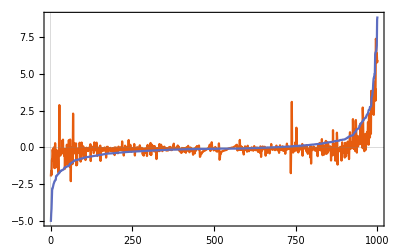

0.440894

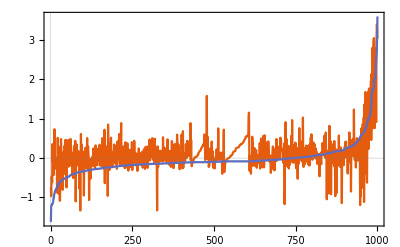

0.172321

```mathematica
tdx=RandomSample[trainingDataS,500];
outActual=Flatten[Table[trained[x],{x,tdx}]];
outTheory=Flatten[Table[x["Output"],{x,tdx}]];
sorted=SortBy[Transpose[{outActual,outTheory}],#[[2]]&];
ListLinePlot[Transpose[sorted],PlotRange->All]
Mean[(outActual-outTheory)^2]

vdx=RandomSample[validationDataS,500];
outActual=Flatten[Table[trained[x],{x,vdx}]];
outTheory=Flatten[Table[x["Output"],{x,vdx}]];
sorted=SortBy[Transpose[{outActual,outTheory}],#[[2]]&];
ListLinePlot[Transpose[sorted],PlotRange->All]
Mean[(outActual-outTheory)^2]

Clear[tdx,vdx,outActual,outTheory,sorted]
```

## Plot learned muh, varh

```mathematica
fourier[offset_,sinCoeffs_,cosCoeffs_,freqs_,tptPlt_]:=Module[
{range,pts}
,
range=Max[Total[Abs[sinCoeffs]+Abs[cosCoeffs]]+10^-8,1];
pts=Table[offset[[1]]+(Sum[sinCoeffs[[i]]*Sin[freqs[[i]]*(tpt-1)]+cosCoeffs[[i]]*Cos[freqs[[i]]*(tpt-1)],{i,Length[freqs]}])/range,{tpt,tptPlt}];

Return[pts];
];
```

{0.0541288,0.0577974,0.0203004,-0.0338641,-0.0289646,-0.0040698}

{0.0108538,0.0368059,0.111482,0.0458398,0.00966856,0.000290326}

{0.00170884,0.0280274,-0.165111,-0.00390174,0.0236238,0.0396789}

{0.0184821,0.105126,0.0985355,-0.128232,-0.0474767,0.00433155}

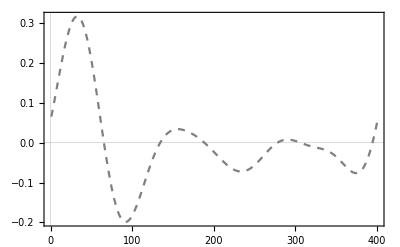

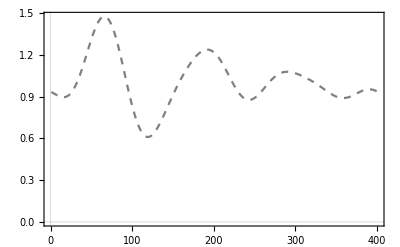

```mathematica
muhOffset=Normal[Information[trained,"Arrays"][{"inputsWOSTD","convert0","layerMuh","offset","Array"}]];
muhCosCoeff=Normal[Information[trained,"Arrays"][{"inputsWOSTD","convert0","layerMuh","cosCoeff","Array"}]]
muhSinCoeff=Normal[Information[trained,"Arrays"][{"inputsWOSTD","convert0","layerMuh","sinCoeff","Array"}]]

varhOffset=Normal[Information[trained,"Arrays"][{"inputsWOSTD","convert0","layerVarh","offset","Array"}]];
varhCosCoeff=
Normal[Information[trained,"Arrays"][{"inputsWOSTD","convert0","layerVarh","cosCoeff","Array"}]]
varhSinCoeff=Normal[Information[trained,"Arrays"][{"inputsWOSTD","convert0","layerVarh","sinCoeff","Array"}]]

tptsPlt=Table[tpt,{tpt,1,dataDesc["noTpts"]}];
ListLinePlot[fourier[muhOffset,muhSinCoeff,muhCosCoeff,freqs,tptsPlt],PlotStyle->{Gray,Dashed},PlotRange->All]
ListLinePlot[fourier[varhOffset,varhSinCoeff,varhCosCoeff,freqs,tptsPlt],PlotStyle->{Gray,Dashed},PlotRange->All]
```

## Calculate STDs

```mathematica
nv=2;
nh=1;
graphCalculateSTDsTrained=makeGraphInputsWOSTD[nv,nh,freqs,muhCosCoeff,muhSinCoeff,varhCosCoeff,varhSinCoeff,rxnSpecs]
```

$Aborted

```mathematica
inputsWOSTDTrained=ConstantArray[0,{Length[ip3sTrain]*dataDesc["noTpts"],Length[rxnSpecs]*5}];

idx=1;
Monitor[
Do[
ip3=ip3sTrain[[i]];

f0=filtered0[ip3]["LD"];
Do[
in=<|
"wt"->f0[[tpt]]["wt"],
"b"->f0[[tpt]]["b"],
"sig2"->f0[[tpt]]["sig2"],
"tpt"->tpt
|>;
inWOSTD=graphCalculateSTDsTrained[in];

inputsWOSTDTrained[[idx]]=inWOSTD;
idx+=1;
,{tpt,dataDesc["noTpts"]}];
,{i,Length[ip3sTrain]}];
,ProgressIndicator[i,{1,Length[ip3sTrain]}]];

rxnsSTDmTrained=Mean[inputsWOSTDTrained];
rxnsSTDvTrained=StandardDeviation[inputsWOSTDTrained];

rxnsSTDmTrained=Table[If[Abs[x]<10^-5,0.0,x],{x,rxnsSTDmTrained}]
rxnsSTDvTrained=Table[If[Abs[x]<10^-5,1.0,x],{x,rxnsSTDvTrained}]

Clear[f0,in,inWOSTD,idx];
```

{-0.357484,0.357484,0.360039,-0.360039,0.360038,0.357484,-0.357484,-0.360039,0.360039,0.360041,1.05803,0.0000132306,-0.91644,0.,-0.0133657,-0.0899285,0.0000132311,0.91644,0.,-0.0133656,0.00309218,0.33293,0.,0.0000278308,0.0032214,0.00309217,-0.338272,0.,-0.0000278308,0.0032214,-0.913282,0.,0.570785,0.,0.285399,0.,0.0000278397,0.,0.335815,0.167914,0.0068784,0.,0.,0.,0.00593022,0.913282,0.,-0.570785,0.,0.285386,0.,-0.0000278397,0.,-0.335815,0.167901,0.0068784,0.,0.,0.,0.00593022}

{0.425605,0.425605,0.390567,0.390567,0.390567,0.425605,0.425605,0.390567,0.390567,0.390566,0.525269,1.,0.238155,1.,0.017312,0.4048,1.,0.238155,1.,0.017312,0.0614681,0.464805,1.,0.113705,0.117704,0.0614681,0.460999,1.,0.113705,0.117703,0.133,1.,0.393743,1.,0.196871,1.,0.0000175314,1.,0.44439,0.222195,0.101806,1.,1.,1.,0.0972827,0.133,1.,0.393743,1.,0.196872,1.,0.0000175314,1.,0.44439,0.222195,0.101806,1.,1.,1.,0.0972827}

```mathematica
rxnsSTDm
rxnsSTDv
```

{-0.357484,0.357484,0.360039,-0.360039,0.360038,0.357484,-0.357484,-0.360039,0.360039,0.360041,0.970018,0.0000191177,-0.893151,0.,-0.0660406,-0.134379,0.0000191188,0.893151,0.,-0.0660427,-0.0717913,0.381355,0.,0.0000270932,-0.0753047,-0.0717913,-0.269859,0.,-0.0000270934,-0.0753047,-0.913282,0.,0.570785,0.,0.285399,0.,0.0000278395,0.,0.335815,0.167914,-0.185217,0.,0.,0.,-0.174054,0.913282,0.,-0.570785,0.,0.285386,0.,-0.0000278395,0.,-0.335815,0.167901,-0.185217,0.,0.,0.,-0.174054}

{0.425605,0.425605,0.390567,0.390567,0.390567,0.425605,0.425605,0.390567,0.390567,0.390566,0.482273,0.0000244424,0.210988,1.,0.1017,0.536469,0.0000244436,0.210988,1.,0.101702,0.261164,0.541662,1.,0.278528,0.38871,0.261164,0.605062,1.,0.278528,0.388706,0.133,1.,0.393743,1.,0.196871,1.,0.0000175311,1.,0.44439,0.222195,0.411248,0.0000149975,1.,1.,0.394287,0.133,1.,0.393743,1.,0.196872,1.,0.0000175311,1.,0.44439,0.222195,0.411248,0.0000149978,1.,1.,0.394287}

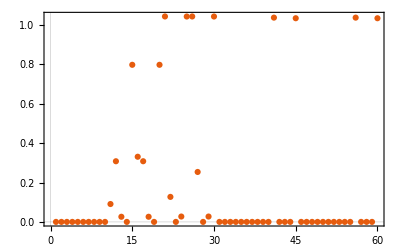

```mathematica
ListPlot[Abs[rxnsSTDm-rxnsSTDmTrained]/(Abs[rxnsSTDm]+10^-12)]
```

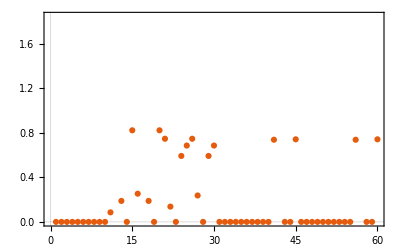

```mathematica
ListPlot[Abs[rxnsSTDv-rxnsSTDvTrained]/(Abs[rxnsSTDv]+10^-12)]
```

```mathematica
inputsSTDTrained=Table[(x-rxnsSTDm)/rxnsSTDv,{x,inputsWOSTDTrained}]
```

{{1.11504,-1.11504,-0.566994,0.566994,-0.566988,-1.11504,1.11504,0.566994,-0.566994,-0.567001,-2.27972,-0.607107,2.54138,0.,32,0.,2.51375,0.,-2.51375,0.,0.207833,0.,1.50006,-1.50006,0.451654,-0.00239207,1.16415×10^-10,-7.10543×10^-15,0.44191},2805,{1}}
 |  |  |  |

```mathematica
Manipulate[
Histogram[inputsSTDTrained[[;;,i]],PlotRange->All]
,{i,1,Length[inputsSTDTrained[[1]]],1}]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Histogram::ldata: Symbol[] is not a valid dataset or list of datasets.

```mathematica
rxnsSTDm
```

{-0.357484,0.357484,0.360039,-0.360039,0.360038,0.357484,-0.357484,-0.360039,0.360039,0.360041,0.970018,0.0000191177,-0.893151,0.,-0.0660406,-0.134379,0.0000191188,0.893151,0.,-0.0660427,-0.0717913,0.381355,0.,0.0000270932,-0.0753047,-0.0717913,-0.269859,0.,-0.0000270934,-0.0753047,-0.913282,0.,0.570785,0.,0.285399,0.,0.0000278395,0.,0.335815,0.167914,-0.185217,0.,0.,0.,-0.174054,0.913282,0.,-0.570785,0.,0.285386,0.,-0.0000278395,0.,-0.335815,0.167901,-0.185217,0.,0.,0.,-0.174054}

```mathematica
Abs[rxnsSTDm-rxnsSTDmTrained]
```

{2.46185×10^-9,2.46185×10^-9,1.8016×10^-10,1.8016×10^-10,4.42735×10^-9,9.23692×10^-10,9.23692×10^-10,8.12875×10^-11,8.12875×10^-11,2.78965×10^-9,0.0819147,5.67761×10^-6,0.0169985,0.,0.0527546,0.0421088,5.67925×10^-6,0.0169985,0.,0.0527566,0.069042,0.0436317,0.,6.45216×10^-7,0.0728747,0.069042,0.0633601,0.,6.4493×10^-7,0.0728747,1.34838×10^-9,0.,4.10087×10^-10,0.,1.59257×10^-11,0.,2.25175×10^-10,0.,0.,0.,0.179876,0.,0.,0.,0.170486,1.34838×10^-9,0.,4.10087×10^-10,0.,2.93033×10^-9,0.,2.25175×10^-10,0.,0.,0.,0.179876,0.,0.,0.,0.170486}

```mathematica
rxnsSTDmTrained
```

{-0.357484,0.357484,0.360039,-0.360039,0.360038,0.357484,-0.357484,-0.360039,0.360039,0.360041,1.05193,0.0000134401,-0.91015,0.,-0.013286,-0.0922707,0.0000134396,0.91015,0.,-0.0132861,-0.00274931,0.337724,0.,0.0000277384,-0.00242999,-0.00274931,-0.333219,0.,-0.0000277383,-0.00242999,-0.913282,0.,0.570785,0.,0.285399,0.,0.0000278397,0.,0.335815,0.167914,-0.00534043,0.,0.,0.,-0.00356743,0.913282,0.,-0.570785,0.,0.285386,0.,-0.0000278397,0.,-0.335815,0.167901,-0.00534042,0.,0.,0.,-0.00356744}

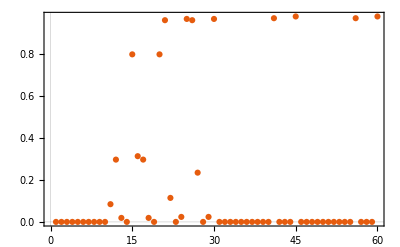

```mathematica
ListPlot[Abs[rxnsSTDm-rxnsSTDmTrained]/(Abs[rxnsSTDm]+10^-12),PlotRange->All]
```

```mathematica
ListPlot[Abs[rxnsSTDm-rxnsSTDmTrained]/(Abs[rxnsSTDmTrained]+10^-12)]
```

```mathematica
outTrained=inputsWOSTDTrained[[1]]
```

{0.117082,-0.117082,0.13859,-0.13859,0.138591,-0.117082,0.117082,-0.13859,0.13859,0.13859,-0.129441,4.25772×10^-6,-0.355737,0.,-0.0746382,0.71271,4.26446×10^-6,0.355737,0.,-0.0746382,4.28408×10^-6,-0.33247,0.,0.0000243167,0.0000136658,4.24683×10^-6,0.332422,0.,-0.0000243167,0.0000136658,-0.353971,0.,-0.418986,0.,-0.209486,0.,0.000024196,0.,-0.330796,-0.165392,0.,0.,0.,0.,0.,0.353971,0.,0.418986,0.,-0.209499,0.,-0.000024196,0.,0.330796,-0.165405,0.,0.,0.,0.,0.}

```mathematica
out=inputsWOSTD[[1]]
```

{0.117082,-0.117082,0.13859,-0.13859,0.138591,-0.117082,0.117082,-0.13859,0.13859,0.13859,-0.163811,4.74838×10^-6,-0.460925,0.,-0.104567,0.875138,4.73469×10^-6,0.460925,-9.09495×10^-13,-0.104569,-0.00915188,-0.302654,-1.86265×10^-9,-0.0608129,-0.0336461,-0.00915186,0.414809,0.,0.0608129,-0.0336486,-0.353971,0.,-0.418986,0.,-0.209486,0.,0.0000241973,0.,-0.330796,-0.165392,0.0276781,-1.89062×10^-6,-1.49012×10^-8,0.,0.00979726,0.353971,0.,0.418986,0.,-0.209499,0.,-0.0000241973,0.,0.330796,-0.165405,0.0276781,-1.8933×10^-6,-3.72529×10^-9,0.,0.00979726}

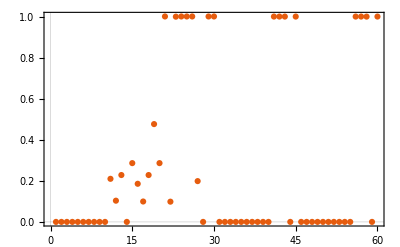

```mathematica
ListPlot[Abs[out-outTrained]/(Abs[out]+10^-12)]
```

```mathematica
rxnsSTDm
rxnsSTDv
```

{-0.357484,0.357484,0.360039,-0.360039,0.360038,0.357484,-0.357484,-0.360039,0.360039,0.360041,1.06314,0.0000131336,-0.917837,0.,-0.00874074,-0.0841192,0.0000131338,0.917837,0.,-0.00874074,0.0000131474,0.337462,0.,0.0000279785,0.0000266947,0.0000131666,-0.337518,0.,-0.0000279785,0.0000266762,-0.913282,0.,0.570785,0.,0.285399,0.,0.0000278397,0.,0.335815,0.167914,0.,0.,0.,0.,0.,0.913282,0.,-0.570785,0.,0.285386,0.,-0.0000278397,0.,-0.335815,0.167901,0.,0.,0.,0.,0.}

{0.425605,0.425605,0.390567,0.390567,0.390567,0.425605,0.425605,0.390567,0.390567,0.390566,0.41545,1.,0.133663,1.,0.0146601,0.376643,1.,0.133663,1.,0.0146601,1.,0.446594,1.,0.0000176187,0.0000187711,1.,0.446619,1.,0.0000176187,0.0000187544,0.133,1.,0.393743,1.,0.196871,1.,0.0000175313,1.,0.44439,0.222195,1.,1.,1.,1.,1.,0.133,1.,0.393743,1.,0.196872,1.,0.0000175313,1.,0.44439,0.222195,1.,1.,1.,1.,1.}

# Integrate

```mathematica
integrate[nv_,nh_,params0_,noTptsIntegrate_,trained_,outMean_,outStd_]:=Module[
{params0St,params0Curr,inputs,derivsS,deriv,derivb,derivwt,derivsig2,params0New,paramsSt,y}
,
params0St={<|"wt"->params0["wt"],"b"->params0["b"],"sig2"->params0["sig2"]|>};
Do[
params0Curr=params0St[[-1]];

inputs=<|
"tpt"->tpt,
"wt"->params0Curr["wt"],
"b"->params0Curr["b"],
"sig2"->{params0Curr["sig2"]}
|>;

derivsS=trained[inputs];
deriv=outStd*derivsS+outMean;

(*
derivb=deriv[[1;;2]];
derivwt={deriv[[3;;4]]};
derivsig2=deriv[[5]];
*)
derivb={deriv[[1]],0.0,0.0};
derivwt={{deriv[[2]],0.0,0.0}};
derivsig2=0.0;

params0New=params0Curr;
params0New["b"]+=derivb;
params0New["wt"]+=derivwt;
params0New["sig2"]+=derivsig2;

AppendTo[params0St,params0New];
,{tpt,noTptsIntegrate}];

paramsSt=Table[y=x;y["muh"]=ConstantArray[0,nh];y["varh"]=IdentityMatrix[nh];y,{x,params0St}];
paramsSt=makePStructFromLD[nv,nh,paramsSt];

Return[paramsSt];
]
```

```mathematica
pltsAll=Association[];
Do[
pltsAll[k]=ListLinePlot[
Table[
filtered0[ip3Key]["LFDL"][k]
,{ip3Key,Join[ip3KeysTraining,ip3KeysValidation]}]
,PlotStyle->LightGray,PlotRange->All]
,{k,{"wt11","b1"}}]
```

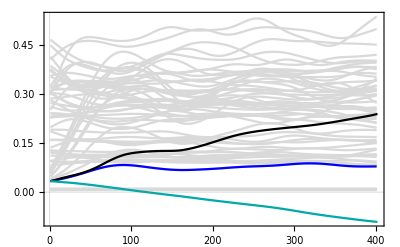
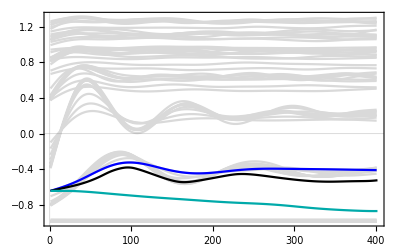

```mathematica
ip3KeyIntegrate={5000,"ip3_0p400"};
params0Start=filtered0[ip3KeyIntegrate]["LD"][[1]];
noTptsIntegrate=dataDesc["noTpts"];

iNet=5;
paramsSt=Association[];
Do[
trained0=Import["trained/"<>mode<>"/"<>IntegerString[iNet,10,2]<>".wlnet"];
paramsSt[mode]=integrate[nv,nh,params0Start,noTptsIntegrate,trained0,outMean,outStd];
,{mode,{"rxns","params"}}];

Table[
Show[
pltsAll[k],
ListLinePlot[filtered0[ip3KeyIntegrate]["LFDL"][k],PlotStyle->Blue,PlotRange->All],
ListLinePlot[{paramsSt["rxns"]["LFDL"][k],paramsSt["params"]["LFDL"][k]},PlotRange->All,PlotStyle->{Black,Darker[Cyan]}],
PlotLabel->labels[k],
PlotRange->All
]
,{k,{"wt11","b1"}}]
```

# MSE

## Integrate & export

```mathematica
(*noIP3RsIntegrate={500,600,700,800,900,1000,1500,2000,2500,3000,3500,4000,4500,5000};*)
noIP3RsIntegrate={100};
ip3sIntegrate={"ip3_0p100","ip3_0p400","ip3_0p700","ip3_1p000","ip3_1p300","ip3_1p600","ip3_1p900"};
modesIntegrate={"rxns","params"};
iStart=1;
iEnd=40;

ip3KeysIntegrate=Flatten[Table[Table[
{noIP3R,ip3Integrate}
,{ip3Integrate,ip3sIntegrate}]
,{noIP3R,noIP3RsIntegrate}],1];
Print[ip3KeysIntegrate];

Do[
Print[mode];

Monitor[
Do[
SetDirectory[NotebookDirectory[]];
trained0=Import["trained/"<>mode<>"/"<>IntegerString[iNet,10,2]<>".wlnet"];

Monitor[
Do[
ip3KeyIntegrate=ip3KeysIntegrate[[i]];
params0Start=filtered0[ip3KeyIntegrate]["LD"][[1]];
noTptsIntegrate=dataDesc["noTpts"];

paramsSt=integrate[nv,nh,params0Start,noTptsIntegrate,trained0,outMean,outStd];

dir="trained/"<>mode<>"/"<>IntegerString[iNet,10,2]<>"_integrated/";
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ[dir],CreateDirectory[dir]];
Export[dir<>IntegerString[ip3KeyIntegrate[[1]],10,4]<>"_"<>ip3KeyIntegrate[[2]]<>".mx",paramsSt]

,{i,Length[ip3KeysIntegrate]}];
,Row[{"ip3key: ",ProgressIndicator[i,{1,Length[ip3KeysIntegrate]}]}]];

,{iNet,iStart,iEnd}];
,Row[{"iNet: ",ProgressIndicator[iNet,{iStart,iEnd}]}]];
,{mode,modesIntegrate}];
```

{{100,ip3_0p100},{100,ip3_0p400},{100,ip3_0p700},{100,ip3_1p000},{100,ip3_1p300},{100,ip3_1p600},{100,ip3_1p900}}

rxns

params

## MSE

```mathematica
getMSEforNoIP3R[iNet_,mode_,filtered0_,noIP3R_,ip3s_]:=Module[
{mse,count,ip3KeyIntegrate,true,actual,paramsSt}
,
mse=0.0;
count=0;
Do[
ip3KeyIntegrate={noIP3R,ip3};

paramsSt=Import["trained/"<>mode<>"/"<>IntegerString[iNet,10,2]<>"_integrated/"<>IntegerString[noIP3R,10,4]<>"_"<>ip3<>".mx"];

Do[
true=filtered0[ip3KeyIntegrate]["LFDL"][k];
actual=paramsSt["LFDL"][k][[;;-2]];
mse+=Total[(true-actual)^2];
count+=Length[true];
,{k,{"wt11","b1"}}];

,{ip3,ip3s}];

mse/=count;
Return[mse];
]
```

```mathematica
noIP3RsMSE={500,600,700,800,900,1000,1500,2000,2500,3000,3500,4000,4500,5000};
ip3sMSE={"ip3_0p100","ip3_0p400","ip3_0p700","ip3_1p000","ip3_1p300","ip3_1p600","ip3_1p900"};
modesMSE={"rxns","params"};
iStart=1;
iEnd=40;

mse=Association[];
Do[
Print[mode];
mse[mode]=Association[];

Monitor[
Do[
mse[mode][iNet]=Association[];

SetDirectory[NotebookDirectory[]];
Do[
mse[mode][iNet][noIP3R]=getMSEforNoIP3R[iNet,mode,filtered0,noIP3R,ip3sMSE];
,{noIP3R,noIP3RsMSE}];

,{iNet,iStart,iEnd}];
,Row[{"iNet: ",ProgressIndicator[iNet,{iStart,iEnd}]}]];
,{mode,modesMSE}];
```

rxns

params

```mathematica
mseWithErr=Association[];
mseWithoutErr=Association[];
mseUpper=Association[];
mseLower=Association[];

Do[
mseWithErr[mode]=Association[];
mseWithoutErr[mode]=Association[];
mseUpper[mode]=Association[];
mseLower[mode]=Association[];

Do[
vals=Table[mse[mode][iNet][noIP3R],{iNet,iStart,iEnd}];
m=Mean[vals];
s=1.96*StandardDeviation[vals]/Sqrt[iEnd-iStart+1];
mseWithErr[mode][noIP3R]=Around[m,s];
mseWithoutErr[mode][noIP3R]=m;
mseUpper[mode][noIP3R]=m+s;
mseLower[mode][noIP3R]=m-s;
,{noIP3R,noIP3RsMSE}];
,{mode,modesRun}];
```

```mathematica
cols=<|
"params"->Directive[Opacity[0.15],Darker[Cyan]],
"rxns"->Directive[Opacity[0.2],Gray]
|>;

pShade=Association[];
Do[
valsPlt={
Transpose[{noIP3RsMSE,Values[mseLower[mode]]}],
Transpose[{noIP3RsMSE,Values[mseUpper[mode]]}]
};

pShade[mode]=ListLogPlot[valsPlt,Filling->{1->{{2},{cols[mode],White}}},PlotStyle->Directive["LineOpacity"->0],Joined->True,PlotRange->All]
,{mode,modesRun}];
```

```mathematica
pMean=ListLogPlot[{
Transpose[{noIP3RsMSE,Values[mseWithoutErr["params"]]}],
Transpose[{noIP3RsMSE,Values[mseWithoutErr["rxns"]]}]
},Joined->True,IntervalMarkers->"Bands",PlotStyle->{Darker[Cyan],Black},PlotRange->All];
```

```mathematica
pltOverlay=Graphics[{Opacity[0.05],Blue,Rectangle[{Min[noIP3RsTraining],Log[0.0005]},{Max[noIP3RsTraining],Log[0.5]}]}];
```

```mathematica
pltMSE=Show[
ListLogPlot[{},PlotRange->{Log[0.001],Log[0.1]}],
pltOverlay,
pShade["params"],
pShade["rxns"],
pMean,
PlotRange->{Log[0.0008],Log[0.1]},
FrameLabel->{"# IP3 receptors (IP3Rs)"},
PlotLabel->"MSE"
]
```

-Graphics-

```mathematica
leg=LineLegend[{Black,Darker[Cyan]},{"DBD (rxns)","DBD (params)"}]
```

## Export

```mathematica
SetDirectory[NotebookDirectory[]];
Export["figures/mse.pdf",pltMSE]
Export["figures/mse.png",pltMSE,ImageResolution->200]

Export["figures/mse_leg.pdf",leg]
Export["figures/mse_leg.png",leg,ImageResolution->200]
```

figures/mse.pdf

figures/mse.png

figures/mse_leg.pdf

figures/mse_leg.png

# Range of oscillations

## Import range of oscillations methods

```mathematica
SetDirectory[NotebookDirectory[]<>"../../../stochastic_simulations/oscillation_range/"];
Get["funcs_oscillation_range.m"]
```

## Integrate to get range of oscillation diagram (single no IP3R)

```mathematica
getMeanStd[nv_,nh_,paramsSt_,mv_,sv_]:=Module[
{avogadro,volExp,vol,params0St,momentsLD,moments,muv,varv,muvS,varvS,stdvS,muvC,stdvC,y}
,
avogadro=6.02214076*^23;
volExp=14;
vol=10^(-1*volExp);

(* Convert to moments *)
momentsLD=Table[convertParamsToMoments[nv,x],{x,paramsSt["LD"]}];
moments=makeMStructFromLD[nv,nh,momentsLD];

(* Transform *)
muv=Transpose[{moments["LFDL"]["mu1"],moments["LFDL"]["mu2"],moments["LFDL"]["mu3"]}];
varv=Table[{
{x["var11"],x["var12"],x["var13"]},
{x["var12"],x["var22"],x["var23"]},
{x["var13"],x["var23"],x["var33"]}
},{x,moments["LFLD"]}];

muvS=Table[x*sv+mv,{x,muv}];
varvS=Table[DiagonalMatrix[sv].x.DiagonalMatrix[sv],{x,varv}];
stdvS=Table[Sqrt[Diagonal[x]],{x,varvS}];

muvC=muvS*10^6/(vol*avogadro);
stdvC=stdvS*10^6/(vol*avogadro);

Return[{muvC,stdvC}];
]
```

```mathematica
noIP3RBF=5000;
ip3sBF={"ip3_0p100","ip3_0p400","ip3_0p700","ip3_1p000","ip3_1p300","ip3_1p600","ip3_1p900"}

maxCa2i=Association[];
minCa2i=Association[];

iNetStart=1;
iNetEnd=40;

Do[
Print[mode];
maxCa2i[mode]=Association[];
minCa2i[mode]=Association[];

Monitor[
Do[
maxCa2i[mode][iNet]=Association[];
minCa2i[mode][iNet]=Association[];

Do[
ip3KeyIntegrate={noIP3RBF,ip3};

SetDirectory[NotebookDirectory[]];
paramsSt=Import["trained/"<>mode<>"/"<>IntegerString[iNet,10,2]<>"_integrated/"<>IntegerString[noIP3RBF,10,4]<>"_"<>ip3<>".mx"];

{muvC,stdvC}=getMeanStd[nv,nh,paramsSt,mv,sv];

ca2iUpper=Transpose[muvC+stdvC][[1]];
ca2iLower=Transpose[muvC-stdvC][[1]];

maxCa2i[mode][iNet][ip3]=Max[ca2iUpper[[-100;;]]];
minCa2i[mode][iNet][ip3]=Min[ca2iLower[[-100;;]]];
,{ip3,ip3sBF}];

,{iNet,iNetStart,iNetEnd}];
,ProgressIndicator[iNet,{iNetStart,iNetEnd}]];

,{mode,{"rxns","params"}}];
```

{ip3_0p100,ip3_0p400,ip3_0p700,ip3_1p000,ip3_1p300,ip3_1p600,ip3_1p900}

rxns

params

```mathematica
maxCa2iWithErr=Association[];
minCa2iWithErr=Association[];

Do[
maxCa2iWithErr[mode]=Association[];
minCa2iWithErr[mode]=Association[];

Do[
vals=Table[maxCa2i[mode][iNet][ip3],{iNet,iNetStart,iNetEnd}];
m=Mean[vals];
s=1.96*StandardDeviation[vals]/Sqrt[iNetEnd-iNetStart+1];
maxCa2iWithErr[mode][ip3]=Around[m,s];

vals=Table[minCa2i[mode][iNet][ip3],{iNet,iNetStart,iNetEnd}];
m=Mean[vals];
s=1.96*StandardDeviation[vals]/Sqrt[iNetEnd-iNetStart+1];
minCa2iWithErr[mode][ip3]=Around[m,s];

,{ip3,ip3sBF}];
,{mode,{"rxns","params"}}];
```

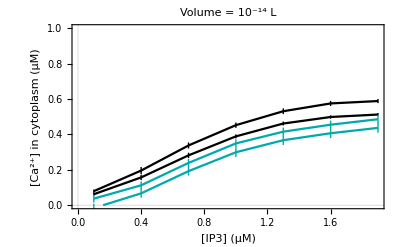

```mathematica
xVals=Table[pStrToNo[x],{x,Keys[maxCa2iWithErr["rxns"]]}];
cols=<|
"rxns"->Black,
"params"->Darker[Cyan]
|>;

pltBifs=Association[];
Do[
pltBifs[mode]=ListLinePlot[{
Transpose[{xVals,Values[maxCa2iWithErr[mode]]}],
Transpose[{xVals,Values[minCa2iWithErr[mode]]}]
},
PlotRange->{0,1},
PlotStyle->cols[mode],
PlotLabel->"Volume = 10^-14 L",
FrameLabel->{"[IP3] (μM)","[Ca^(2+)] in cytoplasm (μM)"}]
,{mode,{"rxns","params"}}];

Show[Values[pltBifs]]
```

## Plot SS

```mathematica
SetDirectory[NotebookDirectory[]<>"oscillation_range_data"];
ca2iMinMaxSS=Import["vol_14_no_ip3r_5000.txt","Table"];

ca2iMinSS=Association[];
ca2iMaxSS=Association[];
Do[
ca2iMinSS[x[[1]]]=x[[2]];(*Around[x[[2]],x[[3]]];*)
ca2iMaxSS[x[[1]]]=x[[4]];(*Around[x[[4]],x[[5]]];*)
,{x,ca2iMinMaxSS}];

pltSS=ListLinePlot[{
Transpose[{Keys[ca2iMinSS],Values[ca2iMinSS]}][[;;-2]],
Transpose[{Keys[ca2iMaxSS],Values[ca2iMaxSS]}][[;;-2]]
},PlotStyle->{{Red}},PlotRange->{0,1}];
```

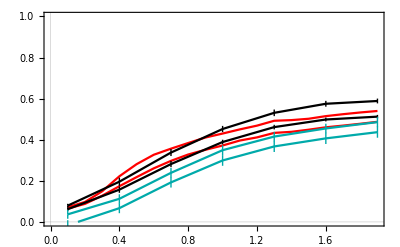

```mathematica
Show[pltSS,Show[Values[pltBifs]]]
```

## Include training range of oscillation diagrams

## Import

```mathematica
SetDirectory[NotebookDirectory[]<>"oscillation_range_data"];
ca2iMins=Association[];
ca2iMaxs=Association[];
Do[
ca2iMinMax=Import["vol_14_no_ip3r_"<>ToString[noIP3R]<>".txt","Table"];
ca2iMins[noIP3R]=Table[x[[2]],{x,ca2iMinMax}];
ca2iMaxs[noIP3R]=Table[x[[4]],{x,ca2iMinMax}];
,{noIP3R,noIP3RsTraining}];
```

## Plot

```mathematica
ip3Vals=Table[pStrToNo[x],{x,ip3s}];
maxmax=Transpose[{ip3Vals,Table[Max[x],{x,Transpose[Values[ca2iMaxs]]}]}];
maxmin=Transpose[{ip3Vals,Table[Min[x],{x,Transpose[Values[ca2iMaxs]]}]}];
minmax=Transpose[{ip3Vals,Table[Max[x],{x,Transpose[Values[ca2iMins]]}]}];
minmin=Transpose[{ip3Vals,Table[Min[x],{x,Transpose[Values[ca2iMins]]}]}];
pltTrain=Show[
ListLinePlot[{maxmin,maxmax},Filling->{1->{{2},{LightBlue,White}}},PlotStyle->Opacity[0]],
ListLinePlot[{minmin,minmax},Filling->{1->{{2},{LightBlue,White}}},PlotStyle->Opacity[0]]
];
```

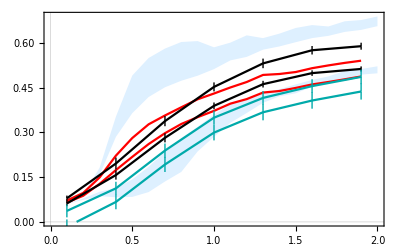

```mathematica
Show[pltTrain,pltSS,Values[pltBifs]]
```